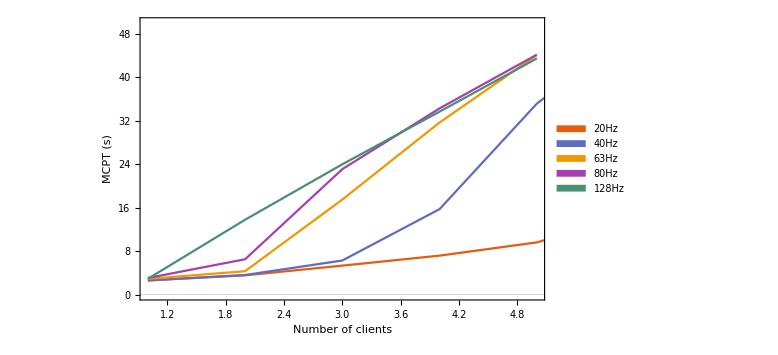

```mathematica
meanchunkprocessingtime128 = {{1,2.9},{2,13.78},{3,24}, {4,33.7},{5,43.5}};
meanchunkprocessingtime80 = {{1,3.05},{2,6.5},{3,23.1},{4,34.3},{5,44.2}};
meanchunkprocessingtime63 = {{1,2.89},{2,4.3},{3,17.5},{4, 31.7},{5,44.12}};
meanchunkprocessingtime20 = {{1,2.6},{2,3.54},{3,5.33},{4, 7.17},{5,9.61},{7,20.15}};
meanchunkprocessingtime40 = {{1,2.6},{2,3.6},{3,6.27},{4, 15.74},{5,35.17}, {6,48.92}};

ListPlot[{meanchunkprocessingtime20,meanchunkprocessingtime40,meanchunkprocessingtime63,meanchunkprocessingtime80, meanchunkprocessingtime128}, Joined->True, AxesLabel->{"Number of clients", "MCPT (s)"},PlotLegends->SwatchLegend[{"20Hz","40Hz", "63Hz","80Hz", "128Hz"}],PlotRange->{{1,5}, {0,50}}, PlotTheme->"Scientific", ImageSize->Large]
```

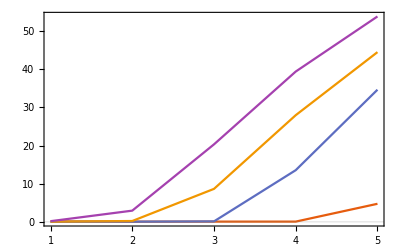

```mathematica
(*40 hertz streaming rate*)
data040 = Import[FileNameJoin[{ParentDirectory[NotebookDirectory[]], "/res/170330032.json"}]];
data140 = Import[FileNameJoin[{ParentDirectory[NotebookDirectory[]], "/res/170330033.json"}]];
data240 = Import[FileNameJoin[{ParentDirectory[NotebookDirectory[]], "/res/170330034.json"}]];
data340 = Import[FileNameJoin[{ParentDirectory[NotebookDirectory[]], "/res/170330035.json"}]];
data440 = Import[FileNameJoin[{ParentDirectory[NotebookDirectory[]], "/res/170330036.json"}]];
datas40 = {data040, data140, data240, data340, data440};
(*62.5 hertz streaming rate*)
data062= Import[FileNameJoin[{ParentDirectory[NotebookDirectory[]], "/res/170330025.json"}]];
data162 = Import[FileNameJoin[{ParentDirectory[NotebookDirectory[]], "/res/170330026.json"}]];
data262 = Import[FileNameJoin[{ParentDirectory[NotebookDirectory[]], "/res/170330027.json"}]];
data362 = Import[FileNameJoin[{ParentDirectory[NotebookDirectory[]], "/res/170330028.json"}]];
data462 = Import[FileNameJoin[{ParentDirectory[NotebookDirectory[]], "/res/170330029.json"}]];
datas62 = {data062, data162, data262, data362, data462};
(*80 hertz streaming rate*)
data080 = Import[FileNameJoin[{ParentDirectory[NotebookDirectory[]], "/res/170330004.json"}]];
data180 = Import[FileNameJoin[{ParentDirectory[NotebookDirectory[]], "/res/170330006.json"}]];
data280 = Import[FileNameJoin[{ParentDirectory[NotebookDirectory[]], "/res/170330008.json"}]];
data380 = Import[FileNameJoin[{ParentDirectory[NotebookDirectory[]], "/res/170330010.json"}]];
data480 = Import[FileNameJoin[{ParentDirectory[NotebookDirectory[]], "/res/170330012.json"}]];
datas80 = {data080, data180, data280, data380, data480};
(*128 hertz streaming rate*)
data0128 = Import[FileNameJoin[{ParentDirectory[NotebookDirectory[]], "/res/170328004.json"}]];
data1128 = Import[FileNameJoin[{ParentDirectory[NotebookDirectory[]], "/res/170328007.json"}]];
data2128 = Import[FileNameJoin[{ParentDirectory[NotebookDirectory[]], "/res/170328010.json"}]];
data3128 = Import[FileNameJoin[{ParentDirectory[NotebookDirectory[]], "/res/170328012.json"}]];
data4128 = Import[FileNameJoin[{ParentDirectory[NotebookDirectory[]], "/res/170328014.json"}]];
datas128 = {data0128, data1128, data2128, data3128, data4128}; 


WSSOH [data_,mcpt_ ] := MapIndexed[Function[{d,i}, Last[d] - mcpt[[i,2]]], data];
OH40 = Flatten[WSSOH[datas40, meanchunkprocessingtime40]];
OH62 = Flatten[WSSOH[datas62, meanchunkprocessingtime63]];
OH80 = Flatten[WSSOH[datas80, meanchunkprocessingtime80]];
OH128 = Flatten[WSSOH[datas128, meanchunkprocessingtime128]];

ListLinePlot[{OH40, OH62, OH80, OH128}, PlotTheme->"Scientific", PlotRange->Full]
```